```mathematica
figDir=FileNameJoin[{NotebookDirectory[],"figures"}];
```

## Districting plans

```mathematica
out=Import["https://mggg.org/uploads/ReCom.pdf",{"PagePositionedObjects",20}];
```

```mathematica
imgs=Import["https://mggg.org/uploads/ReCom.pdf","EmbeddedImages"];
```

```mathematica
g=GraphicsGrid@Partition[ImageCrop@*RemoveBackground/@imgs[[Key[20],15;;-5]],5]
```

-Graphics-

```mathematica
Export[FileNameJoin[{figDir,"plans.png"}],g,Background->Transparent,RasterSize->1500]
```

/Users/christopher/git/census/CVAP/writings/mggg-presentation/figures/plans.png

## Citizenship rate distributions

### Init

Set the Census API key

```mathematica
(*SystemCredential["USCensusAPIKey"]="your Census API key"*)
```

```mathematica
Options[censusQuery]={
Authentication:>SystemCredential["USCensusAPIKey"],
"APIBase"->"api.census.gov"
};
```

```mathematica
censusQuery[path_,query_,opts:OptionsPattern[]]:=
Enclose@Module[{rawResponse,responseList},
rawResponse=Confirm@URLRead@HTTPRequest[<|
"Scheme"->"HTTPS",
"Domain"->OptionValue["APIBase"],
"Path"->path,
"Query"->Join[
query,
{"key"->OptionValue[Authentication]}
]
|>];
responseList=Confirm[Import[rawResponse,"RawJSON"],rawResponse];
ToTabular[Rest@responseList,"Rows",<|"ColumnKeys"->First@responseList|>]
]
```

```mathematica
acsCategoriesCodes=<|
"WhiteAlone"->"A",
"BlackOrAfricanAmericanAlone"->"B",
"AsianAlone"->"D",
"AmericanIndianAndAlaskaNativeAlone"->"C",
"NativeHawaiianAndOtherPacificIslanderAlone"->"E",
"SomeOtherRaceAlone"->"F",
"TwoOrMore"->"G",
"HispanicOrLatino"->"I",
"WhiteAloneNotHispanicOrLatino"->"H",
"Overall"->""
|>;
```

The B05003 tables (Sex by Age by Nativity and Citizenship Status) are the same ones mentioned in Moon's GA expert report.

Get the estimate variables:

```mathematica
getVAPVarsACS[r0_]:=
With[{r=Replace[r0,acsCategoriesCodes]},
{
"B05003"<>r<>"_008E",
"B05003"<>r<>"_019E"
}
]
getVAPVarsACS[r0_List]:=Union@@(getVAPVarsACS/@r0)

getCVAPVarsACS[r0_]:=
With[{r=Replace[r0,acsCategoriesCodes]},
{
"B05003"<>r<>"_009E",
"B05003"<>r<>"_011E",
"B05003"<>r<>"_020E",
"B05003"<>r<>"_022E"
}
]
getCVAPVarsACS[r0_List]:=Union@@(getCVAPVarsACS/@r0)
```

### Experiments

```mathematica
vap=Module[{year="2022",state=Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],vars,t},
vars=getVAPVarsACS["HispanicOrLatino"];
t=CastColumns[
censusQuery[
{"data",year,"acs","acs5"},
{
"get"->StringRiffle[vars,","],
"for"->"tract:*",
"in"->"state:"<>Replace[state,_Entity:>state["FIPSCode"]],
"in"->"county:*"
}
],
vars->"Integer"
];
Normal@Total[t[All,#]&/@vars]
];
```

```mathematica
cvap=Module[{year="2022",state=Entity["AdministrativeDivision",{"Georgia","UnitedStates"}],vars,t},
vars=getCVAPVarsACS["HispanicOrLatino"];
t=CastColumns[
censusQuery[
{"data",year,"acs","acs5"},
{
"get"->StringRiffle[vars,","],
"for"->"tract:*",
"in"->"state:"<>Replace[state,_Entity:>state["FIPSCode"]],
"in"->"county:*"
}
],
vars->"Integer"
];
Normal@Total[t[All,#]&/@vars]
];
```

```mathematica
logBeta[a_,b_]:=LogGamma[a]+LogGamma[b]-LogGamma[a+b]
```

```mathematica
LogLikelihood[BetaBinomialDistribution[α,β,n],{x}]/.Log[Beta[a_,b_]]:>logBeta[a,b]
```

Piecewise[{{Log[Binomial[n,x]]-LogGamma[α]+LogGamma[x+α]-LogGamma[β]+LogGamma[n-x+β]+LogGamma[α+β]-LogGamma[n+α+β], 0≤x≤n}, {-∞, True}}]

```mathematica
betaBinomialLogLikelihood[BetaBinomialDistribution[α_,β_,n_],x_]:=Log[Binomial[n,x]]-LogGamma[α]+LogGamma[x+α]-LogGamma[β]+LogGamma[n-x+β]+LogGamma[α+β]-LogGamma[n+α+β]
```

```mathematica
fitBetaBinomialPrior[super_,sub_]:=
Module[{α,β},
BetaDistribution@@NArgMax[
{
N@Total@betaBinomialLogLikelihood[BetaBinomialDistribution[α,β,super],sub],
0<α,
0<β
},
{α,β}
]
]
```

```mathematica
logSumExp[x0_]:=With[{x=DeleteCases[x0,-Infinity]},{m=Max[x]},If[Length[x]==1,First[x],m+Log[Total@Exp[x-m]]]]
```

```mathematica
fitZeroOneInflatedBetaBinomialPrior[super_,sub_]:=
Module[{ll,α,β,p0,p1,p2},
ll=Total@N@MapThread[
logSumExp[{
If[#2==0,Log[p0/(p0+p1+p2)],-Infinity],
If[#1==#2,Log[p1/(p0+p1+p2)],-Infinity],
Log[p2/(p0+p1+p2)]+betaBinomialLogLikelihood[BetaBinomialDistribution[α,β,#1],#2]
}]&,
{super,sub}
];
{α,β,p0,p1,p2}=NArgMax[{
ll,
0<α,
0<β,
0<=p0<=1,
0<=p1<=1,
0<=p2<=1
},
{α,β,p0,p1,p2}
];
<|
"BetaDistribution"->BetaDistribution[α,β],
"ZeroSpike"->p0/(p0+p1+p2),
"OneSpike"->p1/(p0+p1+p2),
"PDF"->Function[x,Evaluate@PiecewiseExpand@Piecewise[{
{p0/(p0+p1+p2)*DiracDelta[x]+p2/(p0+p1+p2)*PDF[BetaDistribution[α,β],x],x==0},
{p1/(p0+p1+p2)*DiracDelta[x-1]+p2/(p0+p1+p2)*PDF[BetaDistribution[α,β],x],x==1},
{p2/(p0+p1+p2)*PDF[BetaDistribution[α,β],x],True}
}]]
|>
]
```

```mathematica
dist=fitBetaBinomialPrior[vap,cvap]
```

BetaDistribution[0.836377,0.289463]

```mathematica
dist2=ProbabilityDistribution[fitZeroOneInflatedBetaBinomialPrior[vap,cvap]["PDF"][x],{x,0,1}]
```

ProbabilityDistribution[Piecewise[{{0., x>1||x<0}, {1.67086 (1-x)^0.157931 x^0.933916, 0<x<1}, {0.287179 DiracDelta[-1+x], x==1}, {0.0184834 DiracDelta[x], True}}],{x,0,1}]

```mathematica
Mean@dist
```

0.742891

```mathematica
N@Total@cvap/Total@vap
```

0.616492

```mathematica
Quiet@Mean[DeleteCases[N@cvap/vap,Indeterminate]]
```

0.721289

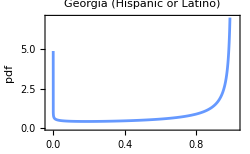

```mathematica
Export[FileNameJoin[{figDir,"empDist0.pdf"}],
Echo@Show[{
Histogram[
Quiet[N@cvap/vap],{0-0.05/2,1+0.05/2,0.05},"PDF",
Frame->True,
FrameLabel->{"ω_t (citizenship rate)","pdf"},
PlotLabel->"Georgia (Hispanic or Latino)",
ChartStyle->Directive[Transparent,EdgeForm[]],
ImageSize->250
],
Plot[Evaluate@{
PDF[dist,x],
Style[PDF[dist2,x],Transparent]
},
{x,0,1},
PlotRange->{{0,1},{0,7}},
PlotStyle->{StandardBlue,StandardRed}
]
}],
Background->Transparent
];
```

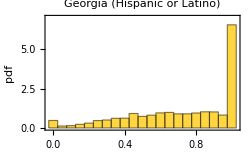

```mathematica
Export[FileNameJoin[{figDir,"empDist1.pdf"}],
Echo@Show[{
Histogram[
Quiet[N@cvap/vap],{0-0.05/2,1+0.05/2,0.05},"PDF",
Frame->True,
FrameLabel->{"ω_t (citizenship rate)","pdf"},
PlotLabel->"Georgia (Hispanic or Latino)",
ImageSize->250
],
Plot[Evaluate@{
Style[PDF[dist,x],Transparent],
Style[PDF[dist2,x],Transparent]
},
{x,0,1},
PlotRange->{{0,1},{0,7}},
PlotStyle->{StandardBlue,StandardRed}
]
}],
Background->Transparent
];
```

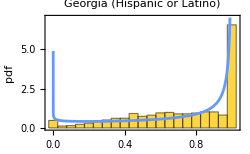

```mathematica
Export[FileNameJoin[{figDir,"empDist2.pdf"}],
Echo@Show[{
Histogram[
Quiet[N@cvap/vap],{0-0.05/2,1+0.05/2,0.05},"PDF",
Frame->True,
FrameLabel->{"ω_t (citizenship rate)","pdf"},
PlotLabel->"Georgia (Hispanic or Latino)",
ImageSize->250
],
Plot[Evaluate@{
PDF[dist,x],
Style[PDF[dist2,x],Transparent]
},
{x,0,1},
PlotRange->{{0,1},{0,7}},
PlotStyle->{StandardBlue,StandardRed}
]
}],
Background->Transparent
];
```

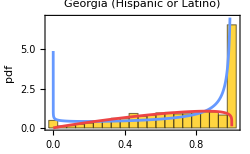

```mathematica
Export[FileNameJoin[{figDir,"empDist3.pdf"}],
Echo@Show[{
Histogram[
Quiet[N@cvap/vap],{0-0.05/2,1+0.05/2,0.05},"PDF",
Frame->True,
FrameLabel->{"ω_t (citizenship rate)","pdf"},
PlotLabel->"Georgia (Hispanic or Latino)",
ImageSize->250
],
Plot[Evaluate@{
PDF[dist,x],
PDF[dist2,x]
},
{x,0,1},
PlotRange->{{0,1},{0,7}},
PlotStyle->{StandardBlue,StandardRed}
]
}],
Background->Transparent
];
```

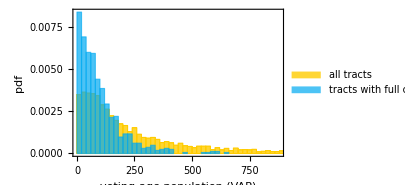

```mathematica
Export[
FileNameJoin[{figDir,"citizenship_pop_hists.pdf"}],
Echo@Histogram[{
Select[vap,#>0&],
Select[Transpose@{cvap,vap},Apply[#1==#2&&#1>0&]][[All,1]]
},100,"PDF",
Frame->True,
FrameLabel->{"voting-age population (VAP)","pdf"},
ChartLegends->Placed[{"all tracts","tracts with full citizenship"},{Right,Top}],
ImageSize->300
],
Background->Transparent
];
```

## Question changes

### Base

Set the Census API key

```mathematica
(*SystemCredential["USCensusAPIKey"]="your Census API key"*)
```

```mathematica
Options[censusQuery]={
Authentication:>SystemCredential["USCensusAPIKey"],
"APIBase"->"api.census.gov"
};
```

```mathematica
censusQuery[path_,query_,opts:OptionsPattern[]]:=
Enclose@Module[{rawResponse,responseList},
rawResponse=Confirm@URLRead@HTTPRequest[<|
"Scheme"->"HTTPS",
"Domain"->OptionValue["APIBase"],
"Path"->path,
"Query"->Join[
query,
{"key"->OptionValue[Authentication]}
]
|>];
responseList=Confirm@Import[rawResponse,"RawJSON"];
ToTabular[Rest@responseList,"Rows",<|"ColumnKeys"->First@responseList|>]
]
```

Get tract-level estimates for a variable:

```mathematica
tractValues[vars_,fipsCode_,path_]:=
Module[{tab},
tab=censusQuery[
path,
{
"get"->StringRiffle[vars,","],
"for"->"tract:*",
"in"->"state:"<>fipsCode,
"in"->"county:*"
}
];
tab=ConstructColumns[tab,
{
"geoid"->Function[#state<>#county<>#tract],
"total"->Function[Total@ToExpression@Lookup[#,vars]]
}
];
GroupBy[FromTabular[tab,"Rows"],Lookup["geoid"]->Lookup["total"],First]
]
```

```mathematica
allStateValues[vars_,path_]:=
Module[{tab},
tab=censusQuery[
path,
{
"get"->StringRiffle[vars,","],
"for"->"state:*"
}
];
tab=ConstructColumns[tab,
{
"geoid"->Function[#state],
"total"->Function[Total@ToExpression@Lookup[#,vars]]
}
];
GroupBy[FromTabular[tab,"Rows"],Lookup["geoid"]->Lookup["total"],First]
]
```

### Comparison

We compute the number of Hispanic White alone people in each tract in Georgia using data from the 5 year ACS (2022 vintage) and the 2020 Decennial Census.

For each, we first get the number of White alone people using the following variables:

ACS: B01001A_001E ("Estimate!!Total:" from "Sex by Age (White Alone)")

Decennial Census: P1_003N ("!!Total:!!Population of one race:!!White alone")

We then get the number of non-Hispanic White alone people using the following variables:

ACS: B01001H_001E ("Estimate!!Total:" from "Sex by Age (White Alone, Not Hispanic or Latino)")

Decennial Census: P2_005N ("!!Total:!!Not Hispanic or Latino:!!Population of one race:!!White alone")

Compute the estimates:

```mathematica
pathACS={"data","2022","acs","acs5"};
pathDec={"data","2020","dec","pl"};
```

```mathematica
fipsCode=Entity["AdministrativeDivision",{"Georgia","UnitedStates"}][EntityProperty["AdministrativeDivision","FIPSCode"]]
```

13

```mathematica
tractCountsACS=
tractValues[{"B01001A_001E"},fipsCode,pathACS]-
tractValues[{"B01001H_001E"},fipsCode,pathACS];
tractCountsDec=
tractValues[{"P1_003N"},fipsCode,pathDec]-
tractValues[{"P2_005N"},fipsCode,pathDec];
```

The results are very different from the ACS and Decennial Census:

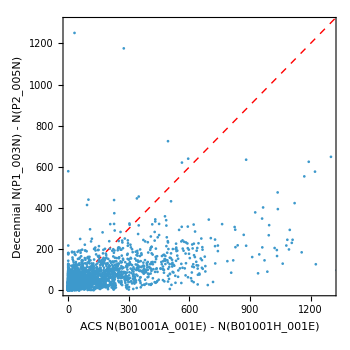

```mathematica
Export[
FileNameJoin[{figDir,"tract_ACS_dec_alignment.pdf"}],
Echo@ListPlot[
Values@Merge[{tractCountsACS,tractCountsDec},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->{{0,1300},{0,1300}},
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"},
ImageSize->350
],
Background->Transparent
];
```

Their distributions are different too. The ACS has far more zero inflation, but also has a fatter tail:

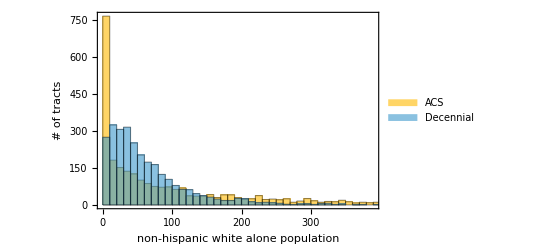

```mathematica
Histogram[{
tractCountsACS,
tractCountsDec
},
{10},
ChartLegends->{"ACS","Decennial"},
Frame->True,FrameLabel->{"non-hispanic white alone population","# of tracts"}
]
```

Comparing the direct variables from the ACS and Decennial Census on their own, they don't look too dissimilar:

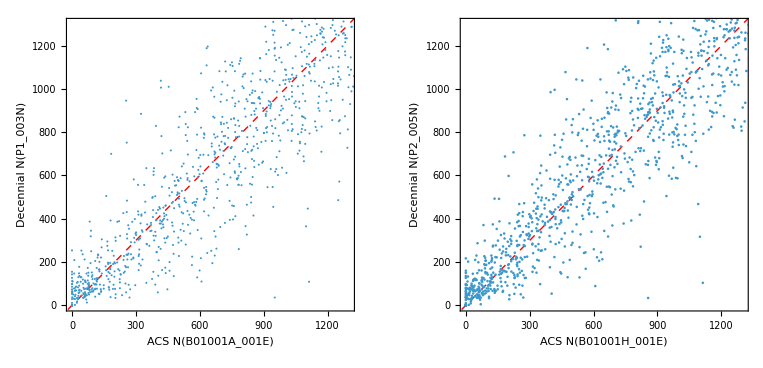

```mathematica
GraphicsRow[{
ListPlot[
Values@Merge[{
tractValues[{"B01001A_001E"},fipsCode,pathACS],
tractValues[{"P1_003N"},fipsCode,pathDec]
},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->{{0,1300},{0,1300}},
Frame->True,
FrameLabel->{"ACS N(B01001A_001E)","Decennial N(P1_003N)"}
],
ListPlot[
Values@Merge[{
tractValues[{"B01001H_001E"},fipsCode,pathACS],
tractValues[{"P2_005N"},fipsCode,pathDec]
},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->{{0,1300},{0,1300}},
Frame->True,
FrameLabel->{"ACS N(B01001H_001E)","Decennial N(P2_005N)"}
]
}]
```

### Statewide

The state-level numbers also disagree:

```mathematica
stateValue[vars_,fipsCode_,path_]:=Total@ToExpression@Normal@censusQuery[path,{"get"->StringRiffle[vars,","],"for"->"state:"<>fipsCode}][[1,vars]]
```

ACS value:

```mathematica
stateValue[{"B01001A_001E"},fipsCode,pathACS]-
stateValue[{"B01001H_001E"},fipsCode,pathACS]
```

374864

Decennial value:

```mathematica
stateValue[{"P1_003N"},fipsCode,pathDec]-
stateValue[{"P2_005N"},fipsCode,pathDec]
```

193327

### Links

https://data.census.gov/table?q=ACSDT5Y2022.B01001A&g=040XX00US13
https://data.census.gov/table?q=ACSDT5Y2022.B01001H&g=040XX00US13

https://data.census.gov/table/DECENNIALPL2020.P1?q=P1&g=040XX00US13
https://data.census.gov/table/DECENNIALPL2020.P2?q=P2&g=040XX00US13

### State-level

```mathematica
pathACS={"data","2022","acs","acs5"};
```

```mathematica
stateCountsACS=
allStateValues[{"B01001A_001E"},pathACS]-
allStateValues[{"B01001H_001E"},pathACS];
stateCountsDec=
allStateValues[{"P1_003N"},pathDec]-
allStateValues[{"P2_005N"},pathDec];
```

```mathematica
fipsStates=AssociationMap[Reverse,EntityValue[EntityClass["AdministrativeDivision","AllUSStatesPlusDC"],"FIPSCode","EntityAssociation"]];
```

```mathematica
Export[
FileNameJoin[{figDir,"state_ACS_dec_alignment.pdf"}],
Echo@ListPlot[
KeyMap[fipsStates,Merge[{stateCountsACS,stateCountsDec},Identity]],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
(*PlotRange->{{0,1300},{0,1300}},*)
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"},
LabelingTarget->"Sparse",
ImageSize->350
],
Background->Transparent
];
```

-Graphics-

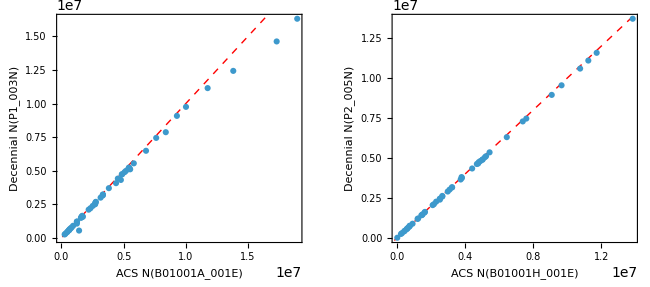

```mathematica
GraphicsRow[{
ListPlot[
Values@Merge[{
allStateValues[{"B01001A_001E"},pathACS],
allStateValues[{"P1_003N"},pathDec]
},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->All,
Frame->True,
FrameLabel->{"ACS N(B01001A_001E)","Decennial N(P1_003N)"}
],
ListPlot[
Values@Merge[{
allStateValues[{"B01001H_001E"},pathACS],
allStateValues[{"P2_005N"},pathDec]
},Identity],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
PlotRange->All,
Frame->True,
FrameLabel->{"ACS N(B01001H_001E)","Decennial N(P2_005N)"}
]
}]
```

### Different vintages

#### 2022 1-year

```mathematica
pathACS={"data","2022","acs","acs1"};
```

```mathematica
stateCountsACS=
allStateValues[{"B01001A_001E"},pathACS]-
allStateValues[{"B01001H_001E"},pathACS];
stateCountsDec=
allStateValues[{"P1_003N"},pathDec]-
allStateValues[{"P2_005N"},pathDec];
```

```mathematica
ListPlot[
KeyMap[fipsStates,Merge[{stateCountsACS,stateCountsDec},Identity]],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
(*PlotRange->{{0,1300},{0,1300}},*)
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"}
]
```

-Graphics-

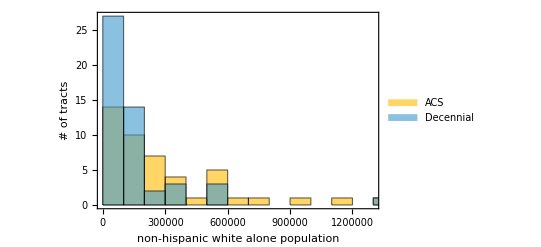

```mathematica
Histogram[{
stateCountsACS,
stateCountsDec
},
{100000},
ChartLegends->{"ACS","Decennial"},
Frame->True,FrameLabel->{"non-hispanic white alone population","# of tracts"}
]
```

#### 2019 1-year

```mathematica
pathACS={"data","2019","acs","acs1"};
```

```mathematica
stateCountsACS=
allStateValues[{"B01001A_001E"},pathACS]-
allStateValues[{"B01001H_001E"},pathACS];
stateCountsDec=
allStateValues[{"P1_003N"},pathDec]-
allStateValues[{"P2_005N"},pathDec];
```

```mathematica
ListPlot[
KeyMap[fipsStates,Merge[{stateCountsACS,stateCountsDec},Identity]],
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
(*PlotRange->{{0,1300},{0,1300}},*)
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"}
]
```

-Graphics-

### Slope over time

```mathematica
getScatterPoints[year_]:=Module[{pathACS,stateCountsACS,stateCountsDec},
pathACS={"data",ToString[year],"acs","acs1"};
stateCountsACS=
allStateValues[{"B01001A_001E"},pathACS]-
allStateValues[{"B01001H_001E"},pathACS];
stateCountsDec=
allStateValues[{"P1_003N"},pathDec]-
allStateValues[{"P2_005N"},pathDec];
KeyMap[fipsStates,Merge[{stateCountsACS,stateCountsDec},Identity]]
]
```

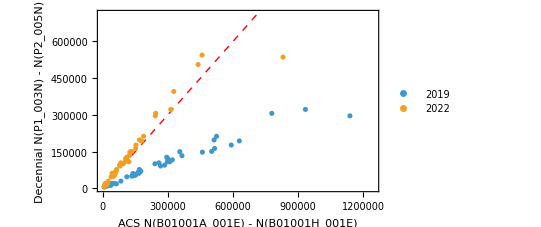

```mathematica
ListPlot[
Values/@{getScatterPoints[2019],getScatterPoints[2022]},
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
(*PlotRange->{{0,1300},{0,1300}},*)
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"},
PlotLegends->Placed[{2019,2022},{Right,Top}]
]
```

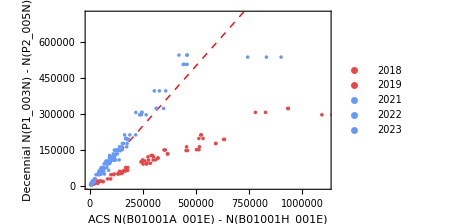

```mathematica
Export[
FileNameJoin[{figDir,"state_1year_ACS_dec_alignment.pdf"}],
Echo@With[{years={2018,2019,2021,2022,2023}},
ListPlot[
Function[y,KeyValueMap[Function[{state,p},Tooltip[p,{state,y}]],getScatterPoints[y]]]/@years,
Epilog->{Red,Dashed,InfiniteLine[{0,0},{1,1}]},
AspectRatio->Automatic,
(*PlotRange->{{0,1300},{0,1300}},*)
Frame->True,
FrameLabel->{"ACS N(B01001A_001E) - N(B01001H_001E)","Decennial N(P1_003N) - N(P2_005N)"},
PlotLegends->Placed[years,{Right,Top}],
PlotStyle->(If[#>=2020,StandardBlue,StandardRed]&/@years),
ImageSize->350
]
],
Background->Transparent
];
```

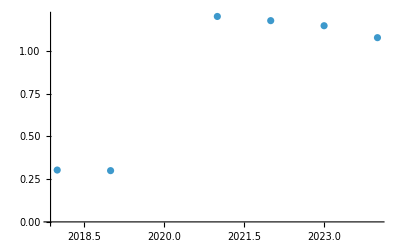

```mathematica
With[{years={2018,2019,2021,2022,2023,2024}},
ListPlot@Transpose[{
years,
LinearModelFit[Values@getScatterPoints[#],x,x]["BestFitParameters"][[2]]&/@years
}]
]
```